# Binomial Fitting

```mathematica
data = {
{1,12105},
{2,42834},
{3,31397},
{4,125874},
{5,95209},
{6,576893}
};
```

```mathematica
sol=FindMinimum[
Sum[(data[[i,2]]-N0 Binomial [6,i] ϵ^i(1-ϵ)^(6-i))^2,{i,1,6}]
,{{ϵ,0.9},{N0,710000}}]
√sol[[1]]
x=sol[[2,1,2]];
n=sol[[2,2,2]];
```

{1.68583×10^10,{ϵ→0.967752,N0→699866.}}

129840.

```mathematica
x=0.8
```

0.8

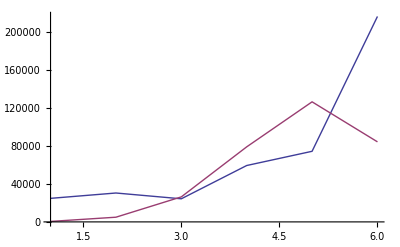

```mathematica
ListPlot[{data, Table[n Binomial [6,i] x^i(1-x)^(6-i),{i,1,6}]},Joined->True]
```